```mathematica
Quit[]
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
(*Load raw MCMC observables.eps is NOT stored as an independent parameter-it is derived from (q0,j0) via the closure relation.eps_mean from the CSV is kept only as "epsMC" for cross-checking.*)BuildModelParamRanges[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName,mkRange},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
mkRange[base_String]:=Module[{mean,plusErr,minusErr},mean=assocFull[base<>"_mean"];
plusErr=assocFull[base<>"_plus"];
minusErr=assocFull[base<>"_minus"];
<|"mean"->mean,"min"->mean-minusErr,"max"->mean+plusErr|>];
datasetName-><|"q0"->mkRange["q0"],"j0"->mkRange["j0"],"Om0"->mkRange["Om0"],"epsMC"->mkRange["eps"]|>]],rows]]];
```

```mathematica
paramRanges3=BuildModelParamRanges[mcmcFiles["Model 3"]];
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParamRanges[file]],mcmcFiles]];
```

```mathematica
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
planckDatasets={"Planck","Planck + Union3","Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

## Setup

## Equations

```mathematica
zPlot=10;
zinitial=1000;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0Func[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 0"->j0Func,"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

#### Determining ϵ from j0

```mathematica
EpsFast["Model 3",q0_?NumericQ,j0_?NumericQ]:= (j0-1)/(3(q0-1/2));
```

### Obtaining q(z)

```mathematica
(*qFnP[model_String,q0Val_?NumericQ,j0Val_?NumericQ,zi_?NumericQ]:=qFnP[model,q0Val,j0Val,zi]=Module[{epsVal,odeQ,sol},epsVal=EpsFast[model,q0Val,j0Val];
odeQ={dq/. j->jModelMap[model]/. {ϵ->epsVal,q0->q0Val,j0->j0Val},q[0]==q0Val};
sol=NDSolve[odeQ,q,{z,0,zi},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];*)
```

Use the closed form of q(z) for faster running times:
dq/dN= (q-1/2)(2q+2-3ϵ)  
u = (q-1/2)/(q+1-3/2 ϵ) --> 	u’=3(1-ϵ)  --> 	1/u du/da=3(1-ϵ) -->	u(z)=u(0) 1/(1+z)^(3(1-ϵ))
q=1/2

```mathematica
qClosed[q0Val_,epsVal_,zz_]:=Module[{u},u=(q0Val-1/2)/(q0Val+1-3/2 epsVal) (1+zz)^(-3 (1-epsVal));
(1/2+u (1-3/2 epsVal))/(1-u)];
```

```mathematica
qFnP["Model 3",q0Val_?NumericQ,j0Val_?NumericQ,zi_?NumericQ]:=With[{ev=EpsFast["Model 3",q0Val,j0Val]},Function[zz,qClosed[q0Val,ev,zz]]];
```

### Obtaining E(z)

```mathematica
EhFnP[model_String,q0Val_?NumericQ,j0Val_?NumericQ,zi_?NumericQ]:=EhFnP[model,q0Val,j0Val,zi]=Module[{epsVal,qFn,odeEh,sol},epsVal=EpsFast[model,q0Val,j0Val];
qFn=qFnP[model,q0Val,j0Val,zi];
odeEh={(dEh/. q->qFn/. {ϵ->epsVal,q0->q0Val}),Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zi},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

### Obtaining Ω_m(z)

## Determining viable trajectories

### Scanning ICs

#### Matter dominated fixed point selection modules

```mathematica
FixedPointsStabilityEps[model_String,epsVal_?NumericQ]:=Module[{jExpr,jAlg,fps,jacMat,jacFn,xx,OO,qq},
jExpr=jModelMap[model][n];
(*substitute onto private symbols:qq,xx,OO cannot collide with the global x,Ω,q used as ODE function names*)
jAlg=(jExpr/. q[n]->qq)/. ϵ->epsVal;
fps=NSolve[{Fx[xx,OO,qq]==0,FΩ[xx,OO,qq]==0,Fq[qq,jAlg]==0},{xx,OO,qq},Reals];
jacMat=D[{Fx[xx,OO,qq],FΩ[xx,OO,qq],Fq[qq,jAlg]},{{xx,OO,qq}}];
jacFn=Function[{xv,Ov,qv},jacMat/. {xx->xv,OO->Ov,qq->qv}];
<|"eps"->epsVal,"jAlg"->jAlg,"fixedPoints"->fps,"vars"->{xx,OO,qq},"Jac"->jacFn|>];
```

```mathematica
MatterDominatedFPEps[model_String,epsVal_?NumericQ]:=MatterDominatedFPEps[model,epsVal]=Module[{fpResult,fps,vars,Jac,ptVals,target,distances,bestIdx,vals,eig,eigvecs,type},fpResult=FixedPointsStabilityEps[model,epsVal];
fps=fpResult["fixedPoints"];vars=fpResult["vars"];
Jac=fpResult["Jac"];
ptVals=Map[N[vars/. #]&,fps];
target=N[{0,1,1/2}];
distances=Map[Norm[#-target]&,ptVals];
bestIdx=First[Ordering[distances,1]];
vals=ptVals[[bestIdx]];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
<|"model"->model,"eps"->epsVal,"jAlg"->fpResult["jAlg"],"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},
eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];
unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];

vxOmega=If[vxOmega[[1]]<0,-vxOmega,vxOmega];
vq=If[vq[[3]]<0,-vq,vq];

<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Module to classify trajectory viability

```mathematica
ClassifyTrajectoryViability[model_String,j0Val_?NumericQ,q0Val_?NumericQ,xFn_,ΩFn_,qFn_,zi_?NumericQ,OptionsPattern[{"NSamples"->150,"SingularTol"->10^-3,"ZMin"->10^-4,"MaxAbsX"->10^3,"MaxOmega"->10,"DomainTol"->10^-8}]]:=Module[{epsVal,nSamples,singTol,zMinSample,maxAbsX,maxOm,domainTol,domain,domainMin,domainMax,zSamples,sampleData,hasSignViolation,hasNearSingular,hasOmegaViolation,hasDivergence,isPhysical,label},
epsVal=EpsFast[model,q0Val,j0Val];
nSamples=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
zMinSample=OptionValue["ZMin"];
maxAbsX=OptionValue["MaxAbsX"];
maxOm=OptionValue["MaxOmega"];
domainTol=OptionValue["DomainTol"];
domain=xFn["Domain"][[1]];
domainMin=domain[[1]];
domainMax=domain[[2]];
(*solution must actually reach z=0 and z=zi-- no extrapolation.DomainTol (strict) judges validity;ZMin only sets sample spacing below.*)If[domainMin>domainTol||domainMax<zi,Return[<|"label"->"Diverged","j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->{}|>]];
zSamples=Prepend[10^Subdivide[Log10[zMinSample],Log10[Min[zi,domainMax]],nSamples-2],0];
sampleData=Table[Module[{xVal,ΩVal,qVal,jVal,denom,ratio,pointLabel},xVal=xFn[zPt];
ΩVal=ΩFn[zPt];
qVal=qFn[zPt];
jVal=(jModelMap[model][zPt]/. ϵ->epsVal)/. q[zPt]->qVal;
denom=jVal-qVal-2;
pointLabel=Which[!(NumericQ[xVal]&&NumericQ[ΩVal]),"Divergent",Abs[xVal]>maxAbsX||ΩVal>maxOm,"Divergent",Abs[denom]<singTol,"NearSingular",ΩVal<=0,"OmegaViolation",xVal/denom<0,"SignViolation",True,"OK"];
ratio=If[Abs[denom]<singTol,Indeterminate,xVal/denom];
<|"z"->zPt,"x"->xVal,"Ω"->ΩVal,"q"->qVal,"j"->jVal,"denom"->denom,"ratio"->ratio,"pointLabel"->pointLabel|>],{zPt,zSamples}];
hasDivergence=AnyTrue[sampleData,#["pointLabel"]==="Divergent"&];
hasNearSingular=AnyTrue[sampleData,#["pointLabel"]==="NearSingular"&];
hasOmegaViolation=AnyTrue[sampleData,#["pointLabel"]==="OmegaViolation"&];
hasSignViolation=AnyTrue[sampleData,#["pointLabel"]==="SignViolation"&];
isPhysical=!(hasDivergence||hasNearSingular||hasOmegaViolation||hasSignViolation);
label=Which[isPhysical,"Physical",hasDivergence,"Divergent",hasNearSingular,"NearSingular",hasOmegaViolation,"OmegaViolation",hasSignViolation,"SignViolation"];
<|"label"->label,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"hasDivergence"->hasDivergence,"hasSignViolation"->hasSignViolation,"hasNearSingular"->hasNearSingular,"hasOmegaViolation"->hasOmegaViolation,"minRatio"->Min[Cases[sampleData[[All,"ratio"]],_?NumericQ]],"minOmega"->Min[sampleData[[All,"Ω"]]],"maxOmega"->Max[sampleData[[All,"Ω"]]],"maxAbsX"->Max[Abs[sampleData[[All,"x"]]]],"minAbsDenom"->Min[Abs[sampleData[[All,"denom"]]]],"domainMin"->domainMin,"domainMax"->domainMax,"sampleData"->sampleData|>];
```

```mathematica
(*Purpose:viability test for one c2,combining the sign condition (a theorem:f_R>0,f_RR>0 require x/(j-q-2)>=0 throughout) with an optional cut on the present-day deviation|x(0)| <=X0Max (a judgement about plausible departure from GR today,since x=dln f_R/dN).Returns both verdicts so the two can be reported separately.*)ViabilityCheck[model_String,q0Val_?NumericQ,j0Val_?NumericQ,c2_?NumericQ,zi_?NumericQ,OptionsPattern[{"X0Max"->1.,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"WorkingPrecision"->30}]]:=Module[{r,signOK,x0},r=Quiet[First@ScanICsP[model,q0Val,j0Val,{c2},zi,"NSamples"->OptionValue["NSamples"],"SingularTol"->OptionValue["SingularTol"],"PrecisionGoal"->OptionValue["PrecisionGoal"],"AccuracyGoal"->OptionValue["AccuracyGoal"],"WorkingPrecision"->OptionValue["WorkingPrecision"]],InterpolatingFunction::dmval];
signOK=(r["label"]==="Physical");
x0=If[signOK,r["sampleData"][[1]]["x"],Missing[]];
<|"signOK"->signOK,"x0"->x0,"bothOK"->(signOK&&Abs[x0]<=OptionValue["X0Max"])|>];
```

#### Scan of ICs

```mathematica
ScanICsP[model_String,q0Val_?NumericQ,j0Val_?NumericQ,c2Range_List,zi_?NumericQ,OptionsPattern[{"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->25,"MaxSteps"->10^8,"WorkingPrecision"->30}]]:=Module[{epsVal,nSamp,singTol,pg,ag,maxSt,wp,fp,cl,vq,vxOmega,qFn,deltaQ,c3},epsVal=EpsFast[model,q0Val,j0Val];
nSamp=OptionValue["NSamples"];
singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];
ag=OptionValue["AccuracyGoal"];
maxSt=OptionValue["MaxSteps"];
wp=OptionValue["WorkingPrecision"];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[Table[<|"c2"->c2,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"DegenerateFP"|>,{c2,c2Range}]]];
vq=cl["vq"];vxOmega=cl["vxOmega"];
qFn=qFnP[model,q0Val,j0Val,zi];
deltaQ=qFn[zi]-fp["q"];
c3=deltaQ/vq[[3]];
Table[Module[{xi,Ωi,sol,xFn,ΩFn,viability},xi=SetPrecision[fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]],wp];
Ωi=SetPrecision[fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]],wp];
sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->pg,AccuracyGoal->ag,MaxSteps->maxSt,WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];
If[!MatchQ[sol,{{__Rule}}],<|"c2"->c2,"xi"->xi,"Ωi"->Ωi,"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"label"->"Failed"|>,(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
viability=ClassifyTrajectoryViability[model,j0Val,q0Val,xFn,ΩFn,qFn,zi,"NSamples"->nSamp,"SingularTol"->singTol];
Join[<|"c2"->c2,"xi"->xi,"Ωi"->Ωi|>,viability])]],{c2,c2Range}]];
```

### Sweeping Xinitial

#### Determine c2 range

```mathematica
AutoC2Scale[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ]:=Module[{fp,classified},fp=MatterDominatedFPEps[model,EpsFast[model,q0Val,j0Val]];
classified=ClassifyEigenvectors[fp];
If[classified===$Failed,$Failed,(1+zi)^(-classified["lambdaXOmega"])]];
```

```mathematica
AutoC2Range[model_String,j0Val_?NumericQ,q0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"LogSpanBelow"->4,"LogSpanAbove"->2,"NPerSign"->40}]]:=Module[{scale,expMin,expMax,positive},scale=AutoC2Scale[model,j0Val,q0Val,zi];
If[scale===$Failed,Return[$Failed]];
expMin=Log10[scale]-OptionValue["LogSpanBelow"];
expMax=Log10[scale]+OptionValue["LogSpanAbove"];
positive=10^Subdivide[expMin,expMax,OptionValue["NPerSign"]-1];
Join[-Reverse[positive],positive]];
```

#### Sweep Xi

```mathematica
(*helper:contiguous index runs of "Physical" points in a results list*)PhysicalRuns[results_List]:=Module[{idx},idx=Flatten[Position[results,r_/;r["label"]==="Physical",{1}]];
If[idx==={},{},Split[idx,#2==#1+1&]]];
```

```mathematica
SweepXInitialP[model_String,q0Val_?NumericQ,j0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"NCoarse"->100,"LogSpanBelow"->3,"LogSpanAbove"->2,"NRefine"->150,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"WorkingPrecision"->30}]]:=Module[{epsVal,nC,nR,nSamp,singTol,pg,ag,wp,coarseRange,nTot,coarseResults,runs,refined,allPts,scanOpts},
epsVal=EpsFast[model,q0Val,j0Val];
nC=OptionValue["NCoarse"];nR=OptionValue["NRefine"];
nSamp=OptionValue["NSamples"];singTol=OptionValue["SingularTol"];
pg=OptionValue["PrecisionGoal"];ag=OptionValue["AccuracyGoal"];
wp=OptionValue["WorkingPrecision"];
scanOpts={"NSamples"->nSamp,"SingularTol"->singTol,"PrecisionGoal"->pg,"AccuracyGoal"->ag,"WorkingPrecision"->wp};
coarseRange=AutoC2Range[model,j0Val,q0Val,zi,"NPerSign"->nC,"LogSpanBelow"->OptionValue["LogSpanBelow"],"LogSpanAbove"->OptionValue["LogSpanAbove"]];
If[coarseRange===$Failed,Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2Window"->None,"table"->{},"note"->"Degenerate fixed point"|>]];
nTot=Length[coarseRange];
coarseResults=ScanICsP[model,q0Val,j0Val,coarseRange,zi,Sequence@@scanOpts];
runs=PhysicalRuns[coarseResults];
If[runs==={},Return[<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->False,"c2Window"->None,"table"->{},"note"->"No physical points in coarse pass"|>]];
refined=Table[Module[{lo,hi,rng,res,phys},lo=coarseRange[[Max[1,First[run]-1]]];
hi=coarseRange[[Min[nTot,Last[run]+1]]];
rng=Subdivide[lo,hi,nR-1];
res=ScanICsP[model,q0Val,j0Val,rng,zi,Sequence@@scanOpts];
phys=Select[res,#["label"]==="Physical"&];
<|"bracket"->{lo,hi},"nPhysical"->Length[phys],"c2Window"->If[phys==={},None,MinMax[phys[[All,"c2"]]]],"points"->Map[<|"c2"->#["c2"],"xi"->#["xi"],"Ωi"->#["Ωi"],"xToday"->#["sampleData"][[1]]["x"],"ΩToday"->#["sampleData"][[1]]["Ω"]|>&,phys]|>],{run,runs}];
allPts=Flatten[refined[[All,"points"]],1];
<|"j0"->j0Val,"q0"->q0Val,"eps"->epsVal,"found"->Length[allPts]>0,"nCoarse"->Total[Length/@runs],"nRefined"->Length[allPts],"nRuns"->Length[runs],"c2Window"->If[allPts==={},None,MinMax[allPts[[All,"c2"]]]],"windows"->refined[[All,"c2Window"]],"table"->allPts|>];
```

#### Using bisection for faster sweep of grid

```mathematica
(*Purpose:locate the viable c2 window by bisection,tracking two nested criteria."sign" is the theorem-level condition (f_R>0,f_RR>0,i.e.x/(j-q-2)>=0 throughout,plus no divergence or Omega violation)."cut" additionally imposes|x(0)| <=X0Max,a judgement about plausible present-day deviation from GR.The cut window is contained in the sign window,so both are bisected from the same seed;if the seed passes sign but fails the cut,the cut window is bracketed within the sign window instead.Assumes each window is a single interval (check nRuns==1).*)FindWindow[model_String,q0Val_?NumericQ,j0Val_?NumericQ,zi_?NumericQ,OptionsPattern[{"NBisect"->20,"X0Max"->1.,"NSamples"->80,"SingularTol"->10^-3,"PrecisionGoal"->14,"AccuracyGoal"->Infinity,"WorkingPrecision"->30,"NLadder"->8,"MaxExpand"->40}]]:=Module[{epsVal,fp,cl,vq,vxOmega,qFn,c3,xiKin,gain,c2Cut,scale,chk,signQ,bothQ,cands,seed,step,bisect,wSign,wCut,seedCut,inner},epsVal=EpsFast[model,q0Val,j0Val];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[<|"found"->False,"eps"->epsVal,"note"->"DegenerateFP"|>]];
vq=cl["vq"];vxOmega=cl["vxOmega"];gain=vxOmega[[1]];
qFn=qFnP[model,q0Val,j0Val,zi];
c3=(qFn[zi]-fp["q"])/vq[[3]];
xiKin=c3 vq[[1]];
c2Cut=-xiKin/gain;
scale=AutoC2Scale[model,j0Val,q0Val,zi];
chk[c2_]:=ViabilityCheck[model,q0Val,j0Val,c2,zi,"X0Max"->OptionValue["X0Max"],"NSamples"->OptionValue["NSamples"],"SingularTol"->OptionValue["SingularTol"],"PrecisionGoal"->OptionValue["PrecisionGoal"],"AccuracyGoal"->OptionValue["AccuracyGoal"],"WorkingPrecision"->OptionValue["WorkingPrecision"]];
signQ[c2_]:=TrueQ[chk[c2]["signOK"]];
bothQ[c2_]:=TrueQ[chk[c2]["bothOK"]];
cands=Join[{If[xiKin<0,0.,c2Cut (1-10^-3)]},Table[c2Cut (1+10^-k),{k,2,7}],Table[c2Cut (1-10^-k),{k,2,7}],Flatten[Table[{-scale 10^e,scale 10^e},{e,Subdivide[-2,2,OptionValue["NLadder"]-1]}]]];
seed=SelectFirst[cands,signQ,$Failed];
If[seed===$Failed,Return[<|"found"->False,"eps"->epsVal,"q0"->q0Val,"j0"->j0Val,"xiKin"->xiKin,"c2Cut"->c2Cut,"note"->"No viable seed found"|>]];
step=Max[Abs[scale],Abs[seed]]/4;
bisect[pred_,s_]:=Module[{lo,hi,mid,k,nExp,a,b},lo=s;hi=s+step;nExp=0;
While[pred[hi]&&nExp<OptionValue["MaxExpand"],lo=hi;hi=hi+step;nExp++];
Do[mid=(lo+hi)/2;If[pred[mid],lo=mid,hi=mid],{k,OptionValue["NBisect"]}];
b=lo;
hi=s;lo=s-step;nExp=0;
While[pred[lo]&&nExp<OptionValue["MaxExpand"],hi=lo;lo=lo-step;nExp++];
Do[mid=(lo+hi)/2;If[pred[mid],hi=mid,lo=mid],{k,OptionValue["NBisect"]}];
a=hi;
{a,b}];
wSign=bisect[signQ,seed];
If[bothQ[seed],seedCut=seed,inner=Subdivide[wSign[[1]],wSign[[2]],20];
seedCut=SelectFirst[inner,bothQ,$Failed]];
wCut=If[seedCut===$Failed,None,bisect[bothQ,seedCut]];
<|"found"->True,"eps"->epsVal,"q0"->q0Val,"j0"->j0Val,"xiKin"->xiKin,"c2Cut"->c2Cut,"gain"->gain,"seed"->seed,"x0Max"->OptionValue["X0Max"],"c2Window"->wSign,"c2WindowCut"->wCut,"xiWindow"->(xiKin+gain #&/@wSign),"xiWindowCut"->If[wCut===None,None,xiKin+gain #&/@wCut],"cutBinds"->If[wCut===None,True,wCut=!=wSign]|>];
```

### Reconstructing x(z) and Ω(z) for each c2

```mathematica
(*rebuild trajectory in full, returns interpolating functions*)ReSolveTrajectory[model_String,q0Val_?NumericQ,j0Val_?NumericQ,c2_?NumericQ,zi_?NumericQ,OptionsPattern[{"PrecisionGoal"->14,"AccuracyGoal"->25,"MaxSteps"->10^8,"WorkingPrecision"->30}]]:=Module[{epsVal,fp,cl,vq,vxOmega,qFn,deltaQ,c3,xi,Ωi,sol,wp},wp=OptionValue["WorkingPrecision"];
epsVal=EpsFast[model,q0Val,j0Val];
fp=MatterDominatedFPEps[model,epsVal];
cl=ClassifyEigenvectors[fp];
If[cl===$Failed,Return[$Failed]];
vq=cl["vq"];vxOmega=cl["vxOmega"];
qFn=qFnP[model,q0Val,j0Val,zi];
deltaQ=qFn[zi]-fp["q"];
c3=deltaQ/vq[[3]];
xi=SetPrecision[fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]],wp];
Ωi=SetPrecision[fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]],wp];
sol=Block[{q},q[zz_]:=qFn[zz];
Quiet[NDSolve[{dx,dΩ,x[zi]==xi,Ω[zi]==Ωi,WhenEvent[Abs[x[z]]>10^3,"StopIntegration"],WhenEvent[Ω[z]>10,"StopIntegration"],WhenEvent[Ω[z]<0,"StopIntegration"]},{x,Ω},{z,0,zi},PrecisionGoal->OptionValue["PrecisionGoal"],AccuracyGoal->OptionValue["AccuracyGoal"],MaxSteps->OptionValue["MaxSteps"],WorkingPrecision->wp],{NDSolve::ndsz,NDSolve::mxst,NDSolve::precw,NDSolve::ndtol,NDSolve::nlnum,NDSolve::ndcf}]];
If[!MatchQ[sol,{{__Rule}}],$Failed,<|"c2"->c2,"xi"->xi,"Ωi"->Ωi,"eps"->epsVal,"x"->(x/. sol[[1]]),"Ω"->(Ω/. sol[[1]]),"q"->qFn|>]];
```

```mathematica
(*Purpose: build the (q0,j0) pairs for one Figure B panel.Panel "j0" fixes q0 at the mean and walks j0 across its 1-sigma,which varies only the closure;panel "q0" fixes j0 and walks q0,which varies the closure and its boundary condition together.Returns pairs,not eps values,since eps is derived downstream via EpsFast.*)ParamGrid[model_String,dataset_String,vary_String,n_Integer]:=Module[{q=allParams[model,dataset,"q0"],jj=allParams[model,dataset,"j0"]},Switch[vary,"j0",Table[{q["mean"],j0v},{j0v,Subdivide[jj["min"],jj["max"],n-1]}],"q0",Table[{q0v,jj["mean"]},{q0v,Subdivide[q["min"],q["max"],n-1]}]]];
```

### Determining f_R0/(f_R(z_i)), m_0 from findwindow

```mathematica
(*Resolves the two edge trajectories(c2Lo,c2Hi) and reads x(0), Omega(0) off each then forms the derived theory quantities:f_R(0)/f_R(z_i) and m_0
Returns the edge values as {lo, hi} pairs in the same order as c2Window.*)AttachTodayValues[model_String,fw_Association,zi_?NumericQ]:=Module[{q0Val,j0Val,Ei,edges,sols,x0s,Om0s,fr0s,m0s},If[!TrueQ[fw["found"]],Return[fw]];
q0Val=fw["q0"];j0Val=fw["j0"];
Ei=EhFnP[model,q0Val,j0Val,zi][zi];
edges=fw["c2Window"];
sols=ReSolveTrajectory[model,q0Val,j0Val,#,zi]&/@edges;
If[AnyTrue[sols,#===$Failed&],Return[Join[fw,<|"todayFound"->False|>]]];
x0s=#["x"][0]&/@sols;
Om0s=#["Ω"][0]&/@sols;
fr0s=Table[(sols[[k]]["Ωi"] Ei^2)/(Om0s[[k]] (1+zi)^3),{k,2}];
m0s=x0s (1-q0Val)/(j0Val-q0Val-2);
Join[fw,<|"todayFound"->True,"x0"->x0s,"Ω0"->Om0s,"fR0"->fr0s,"m0"->m0s|>]];
```

### Theory quantities

```mathematica
(*f_R(0)/f_R(zi);Om0 cancels identically,so no ΩmFun needed*)FR0FromRow[model_String,q0Val_,j0Val_,zi_,row_Association]:=Module[{Ei},Ei=EhFnP[model,q0Val,j0Val,zi][zi];
(row["Ωi"] Ei^2)/(row["ΩToday"] (1+zi)^3)];
```

```mathematica
M0FromRow[q0Val_,j0Val_,row_Association]:=row["xToday"] (1-q0Val)/(j0Val-q0Val-2);
```

```mathematica
(*theory-space curve:r and m along one trajectory*)
RMOfZ[xFn_,ΩFn_,qFn_,model_,q0Val_,j0Val_,zList_List]:=Module[{epsVal,jOf},epsVal=EpsFast[model,q0Val,j0Val];
jOf[zz_]:=jModelMap[model]/. {q->qFn[zz],ϵ->epsVal,q0->q0Val,j0->j0Val};
Table[With[{qq=qFn[zz],xx=xFn[zz],om=ΩFn[zz]},{(1-qq)/(qq+xx-om),xx (1-qq)/(jOf[zz]-qq-2)}],{zz,zList}]];
```

## Plotting global modules

#### Dataset abbreviation

```mathematica
datasetAbbrev=<|"Planck"->"P","Planck + Union3"->"P+U3","Planck + Pantheon+"->"P+PP","Planck + DESY5"->"P+D5","Planck + Union3 + Pantheon+ + DESY5"->"P+U3+PP+D5"|>;
Abbrev[dataset_String]:=Lookup[datasetAbbrev,dataset,dataset];
```

## Analysis

## Determining singularities of (j_0, q_0) within the 1σ bounds

```mathematica
viablePlanckDatasets={"Planck + Pantheon+","Planck + DESY5","Planck + Union3 + Pantheon+ + DESY5"};
```

j_0-q_0-2 =0 	⇔	j_0=q_0+2

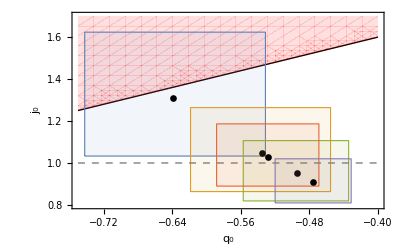

```mathematica
Show[(*viability boundary:j0=q0+2*)Plot[q0v+2,{q0v,-0.75,-0.40},PlotStyle->{Black,Thick},Frame->True,FrameLabel->{"\!\(\*SubscriptBox[\(q\), \(0\)]\)","\!\(\*SubscriptBox[\(j\), \(0\)]\)"},PlotRange->{{-0.75,-0.40},{0.8,1.7}}],(*shade the excluded side*)RegionPlot[j0v>q0v+2,{q0v,-0.75,-0.40},{j0v,0.8,1.7},PlotStyle->Directive[Red,Opacity[0.12]],BoundaryStyle->None],(*1-sigma boxes per dataset*)Graphics[{Table[With[{q=allParams["Model 3",ds,"q0"],jj=allParams["Model 3",ds,"j0"]},{EdgeForm[{Thick,ColorData[97][First@FirstPosition[planckDatasets,ds]]}],FaceForm[Opacity[0.08,ColorData[97][First@FirstPosition[planckDatasets,ds]]]],Rectangle[{q["min"],jj["min"]},{q["max"],jj["max"]}],Black,PointSize[0.012],Point[{q["mean"],jj["mean"]}]}],{ds,planckDatasets}],(*Model 0 reference*)Gray,Dashed,Line[{{-0.75,1},{-0.40,1}}]}]]
```

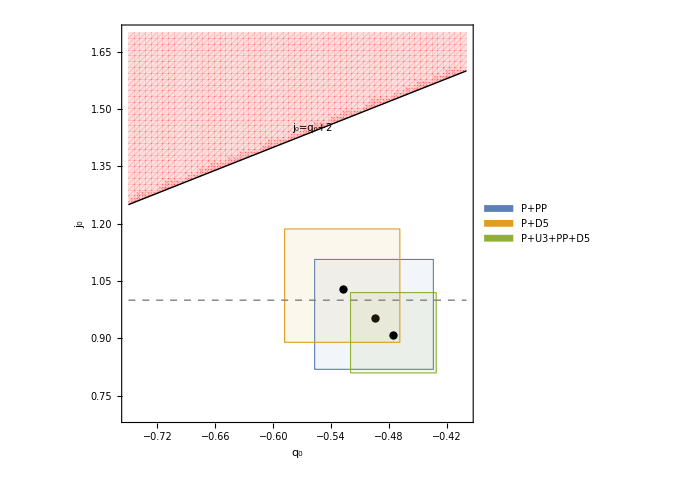

```mathematica
Module[{colors,boxes,legend},colors=ColorData[97]/@Range[Length[viablePlanckDatasets]];
boxes=Table[With[{q=allParams["Model 3",viablePlanckDatasets[[i]],"q0"],jj=allParams["Model 3",viablePlanckDatasets[[i]],"j0"]},{EdgeForm[{Thick,colors[[i]]}],FaceForm[Opacity[0.08,colors[[i]]]],Rectangle[{q["min"],jj["min"]},{q["max"],jj["max"]}],Black,PointSize[0.012],Point[{q["mean"],jj["mean"]}]}],{i,Length[viablePlanckDatasets]}];
legend=SwatchLegend[colors,Abbrev/@viablePlanckDatasets,LegendMarkerSize->14,LegendLabel->None,LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0,Background->White]&)];
Legended[Show[RegionPlot[j0v>q0v+2,{q0v,-0.75,-0.40},{j0v,0.8,1.7},PlotStyle->Directive[Red,Opacity[0.12]],BoundaryStyle->None,PlotPoints->60],Plot[q0v+2,{q0v,-0.75,-0.40},PlotStyle->{Black,Thick}],Graphics[{boxes,Gray,Dashed,Line[{{-0.75,1},{-0.40,1}}],Text[Style["j_0=q_0+2",10,Black],{-0.56,1.45},{0,-1}]}],Frame->True,FrameLabel->{"q_0","j_0"},PlotRange->{{-0.75,-0.40},{0.7,1.7}},ImageSize->500],Placed[legend,{0.2,0.15}]]]
```

## Figure A: m(r) plot

Defined builder functions and variables being used:
qFnP, EpsFast, MatterDominatedFPEps, ClassifyEigenvectors, ReSolveTrajectory, FindWindow, jModelMap, allParams, dx, dΩ, zinitial